```mathematica
(* output of itensor*)
```

```mathematica
X={{0.0000000000,-1.0000000000},{0.0500000000,-1.0006250977},{0.1000000000,-1.0025015664},{0.1500000000,-1.0056329550},{0.2000000000,-1.0100252535},{0.2500000000,-1.0156870128},{0.3000000000,-1.0226295149},{0.3500000000,-1.0308670190},{0.4000000000,-1.0404170857},{0.4500000000,-1.0513010126},{0.5000000000,-1.0635444094},{0.5500000000,-1.0771779806},{0.6000000000,-1.0922385835},{0.6500000000,-1.1087707163},{0.7000000000,-1.1268286668},{0.7500000000,-1.1464797521},{0.8000000000,-1.1678095024},{0.8500000000,-1.1909306578},{0.9000000000,-1.2160008329},{0.9500000000,-1.2432662602},{1.0000000000,-1.2732919051},{1.0500000000,-1.3068579387},{1.1000000000,-1.3428640403},{1.1500000000,-1.3805692336},{1.2000000000,-1.4196174293},{1.2500000000,-1.4597607510},{1.3000000000,-1.5008225096},{1.3500000000,-1.5426672737},{1.4000000000,-1.5851879576},{1.4500000000,-1.6282979624},{1.5000000000,-1.6719260442},{1.5500000000,-1.7160127756},{1.6000000000,-1.7605080229},{1.6500000000,-1.8053690825},{1.7000000000,-1.8505592779},{1.7500000000,-1.8960468812},{1.8000000000,-1.9418042684},{1.8500000000,-1.9878072495},{1.9000000000,-2.0340345350},{1.9500000000,-2.0804672941}};
```

```mathematica
(* exact ground state energy, see e.g. https://member.ipmu.jp/yuji.tachikawa/lectures/2020-komaba/notes6.pdf *)
```

```mathematica
f[h_]:=-NIntegrate[Abs[1- h Exp[2 Pi I s ]],{s,0,1}]
```

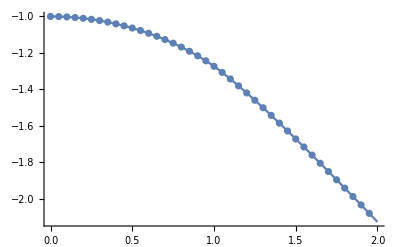

```mathematica
Show[Plot[f[h],{h,0,2}],ListPlot[X]]
```